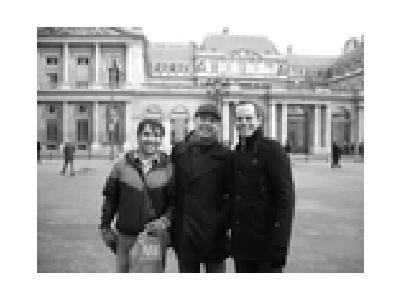
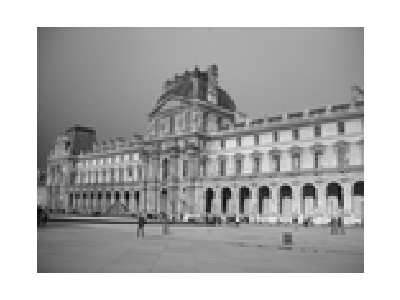

```mathematica
hiddenImage1=StandardiseImage[Import["C:\Users\Julian\secure\My Pictures\Img0030\DSCN0875.jpg"]];
hiddenImage2=StandardiseImage[Import["C:\Users\Julian\secure\My Pictures\Img0030\DSCN0874.jpg"]];
```

```mathematica
A={{.3,.6},{.65,.43}};
```

```mathematica
{signal1,signal2}=A.{Flatten[hiddenImage1],Flatten[hiddenImage2]};
```

```mathematica
sig={signal1,signal2};
```

```mathematica
scaledKurtosis[data_]:=Mean[((data-Mean[data])/StandardDeviation[data])^4]-3
```

```mathematica
t1=Table[
Abs[scaledKurtosis[{w1,1}.sig]],
{w1,-3,3,.1}];
```

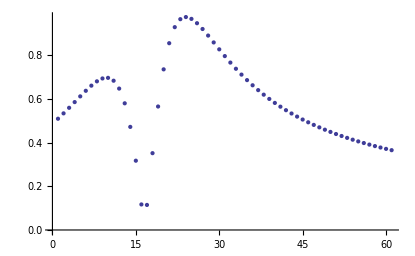

```mathematica
ListPlot[t1]
```

```mathematica
{{-2.1,1},
{-0.7,1}}//Inverse
```

{{-0.714286,0.714286},{-0.5,1.5}}

```mathematica
r1=-({-2.1,1}.sig);
r2=({-.7,1}.sig);
```

```mathematica
{{Min[r1],Max[r1]},{Min[r2],Max[r2]}}
```

{{0.0114118,0.759137},{0.00564706,0.446784}}

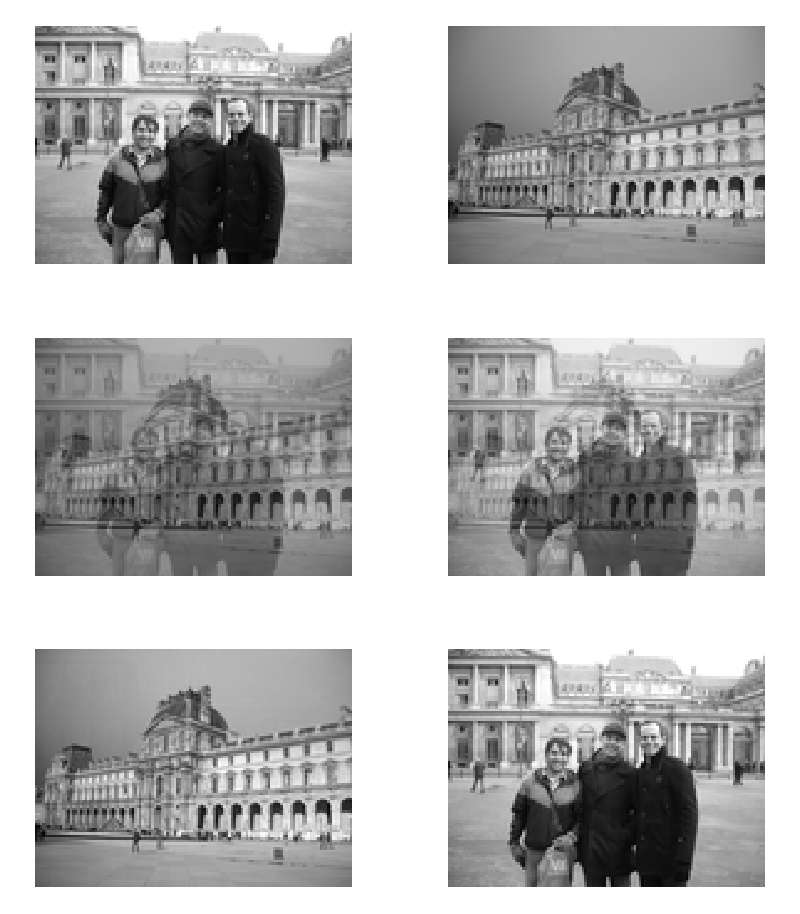

```mathematica
GraphicsGrid[{Map[DispImage,{hiddenImage1,hiddenImage2}],
Map[DispImage[Partition[#,128]]&,{signal1,signal2}],
{Partition[r1/.76,128]//DispImage,
Partition[r2/.44,128]//DispImage}}]
```